```mathematica
DInterpolate[x1_, x2_, y1_, y2_, x1y1_, x1y2_, x2y1_,x2y2_, x_, y_ ]:= (x1y1+(x-x1)*((x2y1-x1y1)/(x2-x1)))+(y-y1)(x1y2+((x-x1)*((x2y2-x1y2)/(x2-x1)))-(x1y1+(x-x1)*((x2y1-x1y1)/(x2-x1))))/(y2-y1)

Interpolate[x1_, x2_, x1y2_, x2y2_, x_] := x1y2+((x-x1)*((x2y2-x1y2)/(x2-x1)))
```

```mathematica
DInterpolate[0.9,0.93,0.1,0.25,-0.126,-0.339,-0.118,-0.315,0.924,0.132]
```

-0.162309

```mathematica
Interpolate[0.93,0.9,-0.118,-0.126,0.924]
```

-0.1196

```mathematica
Solve[(k-m*ω^2)*Ke + ω*c*M == Subscript[F, 0],M]
M=(-k Ke+Ke m ω^2+Subscript[F, 0])/(c ω)

A=Solve[-ω*c*Ke+(k-m*ω^2)*M== 0,Ke]
```

Solve::ivar: (-k Ke+Ke m ω^2+F_0)/(c ω) is not a valid variable.

Solve[-k Ke+Ke m ω^2+Ke (k-m ω^2)+F_0==F_0,(-k Ke+Ke m ω^2+F_0)/(c ω)]

(-k Ke+Ke m ω^2+F_0)/(c ω)

{{Ke→((k-m ω^2) F_0)/(k^2+c^2 ω^2-2 k m ω^2+m^2 ω^4)}}

```mathematica
Simplify[A]
```

{{Ke→((k-m ω^2) F_0)/(k^2+c^2 ω^2-2 k m ω^2+m^2 ω^4)}}

```mathematica
Solve[0.00066== Ki*(140^8.5)*Exp[-Q/(8.314*1090)]]
Q=447016.19525778556+9062.26 Log[Ki]

Solve[0.088== Ki*(140^8.5)Exp[-Q/(8.314*1200)],Ki]
```

{{Q→447016.+9062.26 Log[Ki]}}

447016.+9062.26 Log[Ki]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Ki→57.3595}}

SetDelayed::write: Tag Plus in (447016.+9062.26 Log[Ki])[Ki_] is Protected.

$Failed

(447016.+9062.26 Log[Ki])[57.3595]

```mathematica
447016.19525778556+9062.26* Log[57.36]
```

483712.

```mathematica
Clear[Q]
NSolve[{0.088== Ki*(140^8.5)Exp[-Q/(8.314*1200)],0.00066== Ki*(140^8.5)*Exp[-Q/(8.314*1090)]},{Ki,Q},Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ki→57.3595,Q→483712.}}

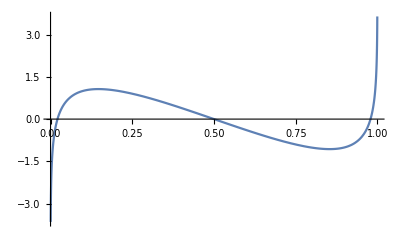

```mathematica
Plot[Log[Exp[1],x]-Log[Exp[1],1-x]+4-8x==0,{x,0,1}]
```

```mathematica
Solve[Log[Exp[1],x]-Log[Exp[1],1-x]+4-8x==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[4-8 x-Log[1-x]+Log[x]==0,x]

```mathematica
Interpolate[x1_, x2_, x1y2_, x2y2_, x_] := x1y2+((x-x1)*((x2y2-x1y2)/(x2-x1)))
```

```mathematica
Interpolate[550,600,6.8778,7.0205,560]
```

6.90634

```mathematica
Interpolate[6.8293,7.0316,2935.01,3045.80,6.90634]
```

2977.2

```mathematica
Solve[(1-x)*7.9085+0.8319*x== 6.906,x]
```

{{x→0.141664}}

```mathematica
Solve[Sqrt[5-x]== 5-x^2,x]
```

{{x→1/2 (1-√17)},{x→1/2 (-1+√21)}}

```mathematica
0.008314∫_313^307 (1.702+9.081*10^-3*T-2.164*10^-6*T^2)ⅆT
```

-0.214957

```mathematica
DInterpolate[x1_, x2_, y1_, y2_, x1y1_, x1y2_, x2y1_,x2y2_, x_, y_ ]:= (x1y1+(x-x1)*((x2y1-x1y1)/(x2-x1)))+(y-y1)(x1y2+((x-x1)*((x2y2-x1y2)/(x2-x1)))-(x1y1+(x-x1)*((x2y1-x1y1)/(x2-x1))))/(y2-y1)
```

```mathematica
DInterpolate[1.6,1.7,0.25,0.5,-0.107,-0.216,-0.096,-0.192,1.6422,0.4348]
```

```mathematica
-0.17887554879999998*0.008314*190.6
```

-0.283455

```mathematica
DInterpolate[1.6,1.7,0.1,0.25,-0.043,-0.107,-0.038,-0.096,1.61,0.1087]
```

```mathematica
-0.046177199999999995*0.008314*190.6
```

-0.0731746

```mathematica
-0.28345485220504185-(-0.07317462609647998)
```

-0.21028

Clear::wrsym: Symbol Tr is Protected.

```mathematica
b1=0.1181193
b2=0.265728
b3=0.154790
b4=0.030323
c1=0.0236744
c2=0.0186984
c3=0
c4=0.042724
d1=0.155488*10^-4
d2=0.623689*10^-4
β=0.65392
γ=0.060167

B=b1-b2/Tr1-b3/Tr1^2-b4/Tr1^3
Ci= c1-c2/Tr1+c3/Tr1^3
Di=d1+d2/Tr1

b1r=0.2026579
b2r=0.331511
b3r=0.027655
b4r=0.203488
c1r=0.0313385
c2r=0.0503618
c3r=0.016901
c4r=0.041577
d1r=0.48736 *10^-4
d2r=0.0740336*10^-4
βr=1.226
γr=0.03754

Br=b1r-b2r/Tr1-b3r/Tr1^2-b4r/Tr1^3
Cir= c1r-c2r/Tr1+c3r/Tr1^3
Dir=d1r+d2r/Tr1

S=(Pr*Vr1)/Tr1==1+B/Vr1+Ci/Vr1^2+Di/Vr1^5+c1/(Tr1^3*(Vr1)^2)*(β+γ/Vr1^2)*Exp[-γ/Vr1^2]
R= (Pr*VrR1)/Tr1==1+Br/VrR1+Cir/VrR1^2+Dir/VrR1^5+c1r/(Tr1^3*(VrR1)^2)*(βr+γr/VrR1^2)*Exp[-γr/VrR1^2]
```

0.118119

0.265728

0.15479

0.030323

0.0236744

0.0186984

0

0.042724

0.0000155488

0.0000623689

0.65392

0.060167

0.118119-0.030323/Tr1^3-0.15479/Tr1^2-0.265728/Tr1

0.0236744-0.0186984/Tr1

0.0000155488+0.0000623689/Tr1

0.202658

0.331511

0.027655

0.203488

0.0313385

0.0503618

0.016901

0.041577

0.000048736

7.40336×10^-6

1.226

0.03754

0.202658-0.203488/Tr1^3-0.027655/Tr1^2-0.331511/Tr1

0.0313385+0.016901/Tr1^3-0.0503618/Tr1

0.000048736+(7.40336×10^-6)/Tr1

(Pr Vr1)/Tr1==1+(0.0000155488+0.0000623689/Tr1)/Vr1^5+(0.0236744-0.0186984/Tr1)/Vr1^2+(0.0236744 ⅇ^(-0.060167/Vr1^2) (0.65392+0.060167/Vr1^2))/(Tr1^3 Vr1^2)+(0.118119-0.030323/Tr1^3-0.15479/Tr1^2-0.265728/Tr1)/Vr1

(Pr VrR1)/Tr1==1+(0.000048736+(7.40336×10^-6)/Tr1)/VrR1^5+(0.0313385+0.016901/Tr1^3-0.0503618/Tr1)/VrR1^2+(0.0313385 ⅇ^(-0.03754/VrR1^2) (1.226+0.03754/VrR1^2))/(Tr1^3 VrR1^2)+(0.202658-0.203488/Tr1^3-0.027655/Tr1^2-0.331511/Tr1)/VrR1

```mathematica
Manipulate[NSolve[(Pr Vr1)/Tr1==1+(0.0000155488+0.0000623689/Tr1)/Vr1^5+(0.0236744-0.0186984/Tr1)/Vr1^2+(0.0236744 ⅇ^(-0.060167/Vr1^2) (0.65392+0.060167/Vr1^2))/(Tr1^3 Vr1^2)+(0.1181193-0.030323/Tr1^3-0.15479/Tr1^2-0.265728/Tr1)/Vr1,Vr1,PositiveReals],{Pr,0,4},{Tr1,0,4}]
Manipulate[NSolve[(Pr VrR1)/Tr1==1+(0.000048736+(7.403360000000001*^-6)/Tr1)/VrR1^5+(0.0313385+0.016901/Tr1^3-0.0503618/Tr1)/VrR1^2+(0.0313385 ⅇ^(-0.03754/VrR1^2) (1.226+0.03754/VrR1^2))/(Tr1^3 VrR1^2)+(0.2026579-0.203488/Tr1^3-0.027655/Tr1^2-0.331511/Tr1)/VrR1,VrR1,PositiveReals],{Pr,0,4},{Tr1,0,4}]
```

NSolve::bdomv: Warning: Max is not a valid domain specification. Assuming it is a variable to eliminate.

```mathematica
Manipulate[List[Pr/Tr1*Vr1/.NSolve[(Pr Vr1)/Tr1==1+(0.0000155488+0.0000623689/Tr1)/Vr1^5+(0.0236744-0.0186984/Tr1)/Vr1^2+(0.0236744 ⅇ^(-0.060167/Vr1^2) (0.65392+0.060167/Vr1^2))/(Tr1^3 Vr1^2)+(0.1181193-0.030323/Tr1^3-0.15479/Tr1^2-0.265728/Tr1)/Vr1,Vr1,PositiveReals][[1]], ((Pr/Tr1*VrR1/.NSolve[(Pr VrR1)/Tr1==1+(0.000048736+(7.403360000000001*^-6)/Tr1)/VrR1^5+(0.0313385+0.016901/Tr1^3-0.0503618/Tr1)/VrR1^2+(0.0313385 ⅇ^(-0.03754/VrR1^2) (1.226+0.03754/VrR1^2))/(Tr1^3 VrR1^2)+(0.2026579-0.203488/Tr1^3-0.027655/Tr1^2-0.331511/Tr1)/VrR1,VrR1,PositiveReals][[1]])-(Pr/Tr1*Vr1/.NSolve[(Pr Vr1)/Tr1==1+(0.0000155488+0.0000623689/Tr1)/Vr1^5+(0.0236744-0.0186984/Tr1)/Vr1^2+(0.0236744 ⅇ^(-0.060167/Vr1^2) (0.65392+0.060167/Vr1^2))/(Tr1^3 Vr1^2)+(0.1181193-0.030323/Tr1^3-0.15479/Tr1^2-0.265728/Tr1)/Vr1,Vr1,PositiveReals][[1]]))*1/0.3978, (Pr/Tr1*Vr1/.NSolve[(Pr Vr1)/Tr1==1+(0.0000155488+0.0000623689/Tr1)/Vr1^5+(0.0236744-0.0186984/Tr1)/Vr1^2+(0.0236744 ⅇ^(-0.060167/Vr1^2) (0.65392+0.060167/Vr1^2))/(Tr1^3 Vr1^2)+(0.1181193-0.030323/Tr1^3-0.15479/Tr1^2-0.265728/Tr1)/Vr1,Vr1,PositiveReals][[1]])+((Pr/Tr1*VrR1/.NSolve[(Pr VrR1)/Tr1==1+(0.000048736+(7.403360000000001*^-6)/Tr1)/VrR1^5+(0.0313385+0.016901/Tr1^3-0.0503618/Tr1)/VrR1^2+(0.0313385 ⅇ^(-0.03754/VrR1^2) (1.226+0.03754/VrR1^2))/(Tr1^3 VrR1^2)+(0.2026579-0.203488/Tr1^3-0.027655/Tr1^2-0.331511/Tr1)/VrR1,VrR1,PositiveReals][[1]])-(Pr/Tr1*Vr1/.NSolve[(Pr Vr1)/Tr1==1+(0.0000155488+0.0000623689/Tr1)/Vr1^5+(0.0236744-0.0186984/Tr1)/Vr1^2+(0.0236744 ⅇ^(-0.060167/Vr1^2) (0.65392+0.060167/Vr1^2))/(Tr1^3 Vr1^2)+(0.1181193-0.030323/Tr1^3-0.15479/Tr1^2-0.265728/Tr1)/Vr1,Vr1,PositiveReals][[1]]))*ω/0.3978],{Pr,0,10},{Tr1,0,10},{ω,0,1}]
```